```mathematica
s=.
w=.
Pi
HoldForm[Integrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(x/s)^2]*Exp[-Integrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(t/s)^2],{t, -Infinity, x}]], {x,-Infinity, Infinity}]]
{{Integrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(x/s)^2]*Exp[-Integrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(t/s)^2],{t, -Infinity, x}]], {x,-Infinity, Infinity}]}, {□}}
```

π

∫_(-∞)^∞ (w Exp[-0.5 (x/s)^2] Exp[-∫_(-∞)^x (w Exp[-0.5 (t/s)^2])/(s √(2 π))ⅆt])/(s √(2 π))ⅆx

{{∫_(-∞)^∞ ConditionalExpression[(ⅇ^(-(0.5 x^2)/s^2-(w (1.25331/(√(1/s^2))+(1.25331 x Erf[0.707107 √(x^2/s^2)])/(√(x^2/s^2))))/(√(2 π) s)) w)/(√(2 π) s),Re[s^2]>0]ⅆx},{□}}

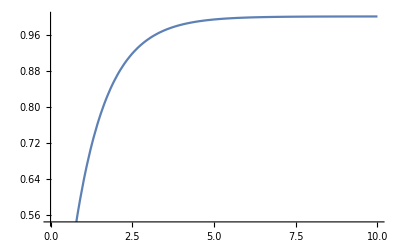

```mathematica
Plot[NIntegrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(x/s)^2]*Exp[-Integrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(t/s)^2],{t, -Infinity, x}]], {x,-Infinity, Infinity}], {w, 0, 10}]
```

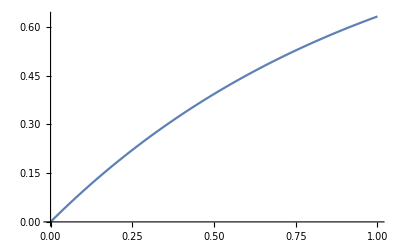

```mathematica
Plot[NIntegrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(x/s)^2]*Exp[-Integrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(t/s)^2],{t, -Infinity, x}]], {x,-Infinity, Infinity}], {w, 0, 1}]
```

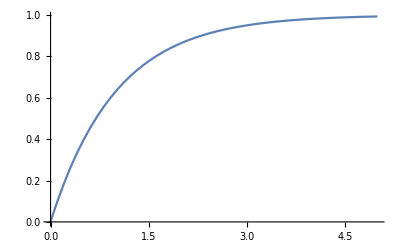

```mathematica
Plot[{1-Exp[-w]}, {w, 0, 5}]
```

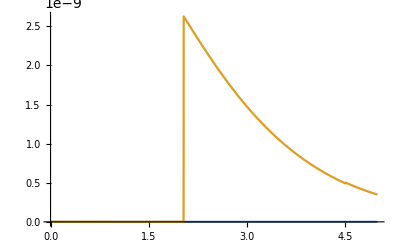

```mathematica
Plot[{0,NIntegrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(x/s)^2]*Exp[-Integrate[(w/(s*Sqrt[2*Pi]))*Exp[-0.5*(t/s)^2],{t, -Infinity, x}]], {x,-Infinity, Infinity}]}, {w, 0, 5}]
```